```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
(*AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]*)
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
Print[Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL,zta}]]//OutputForm]
```

{{-4, ⟨0.786(34)⟩_(2902J)}, {-3, ⟨0.540(12)⟩_(2902J)}, {-2, ⟨0.2944(36)⟩_(2902J)}, {-1, ⟨0.09077(75)⟩_(2902J)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>0.001},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

## Main Code:

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

### A2B fits

```mathematica
FitetarangeList[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];

(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,j_}]:=(a*Exp[-f*x1])/(1+c*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{nparam,1.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,j}],"{a,c,d,f,j}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,g_,j_}]:=(a*Exp[-f*x1])/(1+c*x2^2+d*(x1^g)*x3^2)^j;
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,g,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{g,0.8},{nparam,1.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,g,j}],"{a,c,d,f,g,j}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];
*)

 (*xhi^2  = 1.10902*)
(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,g_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(x1^g))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,g,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{g,0.8},{nparam,1.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,g,j}],"{a,c,d,f,g,j}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];
*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k_,j_}]:=(a*Exp[-0.52*x1])/(1+(d+c*(1-(k*x1^(-1))))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k,nparam}],{{a,5.3},{c,0.052},{d,0.103},{k,7.73},{nparam,2.6}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,k,j}],"{a,c,d,k,j}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];
(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k,j}],"{a,c,d,f,k,j}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];
*)
Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeList[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.52 η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,k,j} | {⟨6.2(10)⟩_(2902J), ⟨0.036(17)⟩_(2902J), ⟨0.104(29)⟩_(2902J), ⟨7.85(97)⟩_(2902J), ⟨2.16(20)⟩_(2902J)} | 1.15859

```mathematica
FitetarangeList[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.5 η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,k,j} | {⟨5.29(85)⟩_(2902J), ⟨0.052(19)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨7.81(62)⟩_(2902J), ⟨2.16(20)⟩_(2902J)} | 1.13564

```mathematica
FitetarangeList[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+c b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨7.4(15)⟩_(2902J), ⟨0.104(27)⟩_(2902J), ⟨0.107(30)⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨2.14(20)⟩_(2902J)} | 1.26666
a ⅇ^(-f η) (1+(d+c (1-k η^-g)) b_L^2+d b_T^2)^-j | {a,c,d,f,g,k,j} |              3                                               6                                              6                                              6                                              9                                             9                                               3
{⟨32(33) × 10 ⟩_(2902J), ⟨-1.45(53) × 10 ⟩_(2902J), ⟨-4.4(45) × 10 ⟩_(2902J), ⟨-2.7(27) × 10 ⟩_(2902J), ⟨-6.8(69) × 10 ⟩_(2902J), ⟨3.7(38) × 10 ⟩_(2902J), ⟨-400(410) × 10 ⟩_(2902J)} | 1.23974

```mathematica
FitetarangeList[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+c b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨7.4(15)⟩_(2902J), ⟨0.104(27)⟩_(2902J), ⟨0.107(30)⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨2.14(20)⟩_(2902J)} | 1.26666
a ⅇ^(-f η) (1+(d+c η^g) b_L^2+d b_T^2)^-j | {a,c,d,f,g,j} |                                                         6                                                                                                                                6
{⟨6.7(11)⟩_(2902J), ⟨-39.3(39) × 10 ⟩_(2902J), ⟨0.093(22)⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨42(25) × 10 ⟩_(2902J), ⟨2.23(20)⟩_(2902J)} | 1.32235
a ⅇ^(-f η) (1+(d+c (1-k η^-g)) b_L^2+d b_T^2)^-j | {a,c,d,f,g,k,j} |                                                           6
{⟨11.0(26)⟩_(2902J), ⟨-1.680(72) × 10 ⟩_(2902J), ⟨0.229(82)⟩_(2902J), ⟨0.563(29)⟩_(2902J), ⟨59.35(75)⟩_(2902J), ⟨127.7(17)⟩_(2902J), ⟨0.72(97)⟩_(2902J)} | 1.86089
a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k,j} | {⟨5.3(12)⟩_(2902J), ⟨0.052(21)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.501(15)⟩_(2902J), ⟨7.73(67)⟩_(2902J), ⟨2.16(21)⟩_(2902J)} | 1.1098

```mathematica
FitetarangeList[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+c b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨7.4(15)⟩_(2902J), ⟨0.104(27)⟩_(2902J), ⟨0.107(30)⟩_(2902J), ⟨0.541(12)⟩_(2902J), ⟨2.14(20)⟩_(2902J)} | 1.26666
a ⅇ^(-f η) (1+c b_L^2+d η^g b_T^2)^-j | {a,c,d,f,g,j} | {⟨8.6(26)⟩_(2902J), ⟨0.110(33)⟩_(2902J), ⟨0.148(96)⟩_(2902J), ⟨0.559(22)⟩_(2902J), ⟨-0.19(19)⟩_(2902J), ⟨2.09(20)⟩_(2902J)} | 1.24404
a ⅇ^(-f η) (1+c η^g b_L^2+d b_T^2)^-j | {a,c,d,f,g,j} | {⟨5.2(12)⟩_(2902J), ⟨0.034(17)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.500(15)⟩_(2902J), ⟨0.50(15)⟩_(2902J), ⟨2.16(21)⟩_(2902J)} | 1.10902
a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k,j} | {⟨5.3(12)⟩_(2902J), ⟨0.052(21)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.501(15)⟩_(2902J), ⟨7.73(67)⟩_(2902J), ⟨2.16(21)⟩_(2902J)} | 1.1098

```mathematica
FitetarangeList[3,-2,7,10]
```

Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+c b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨5.3(19)⟩_(2902J), ⟨0.047(30)⟩_(2902J), ⟨0.048(33)⟩_(2902J), ⟨0.563(24)⟩_(2902J), ⟨3.05(98)⟩_(2902J)} | 0.908308
a ⅇ^(-f η) (1+c b_L^2+d η^g b_T^2)^-j | {a,c,d,f,g,j} | {⟨6.7(46)⟩_(2902J), ⟨0.051(36)⟩_(2902J), ⟨0.05 ± 0.16⟩_(2902J), ⟨0.602(50)⟩_(2902J), ⟨-0.37(40)⟩_(2902J), ⟨2.89(93)⟩_(2902J)} | 0.892823
a ⅇ^(-f η) (1+c η^g b_L^2+d b_T^2)^-j | {a,c,d,f,g,j} | {⟨3.3(15)⟩_(2902J), ⟨0.01 ± 0.013⟩_(2902J), ⟨0.046(32)⟩_(2902J), ⟨0.506(30)⟩_(2902J), ⟨0.62(29)⟩_(2902J), ⟨3.1(11)⟩_(2902J)} | 0.841779
a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k,j} | {⟨3.4(15)⟩_(2902J), ⟨0.030(22)⟩_(2902J), ⟨0.046(33)⟩_(2902J), ⟨0.510(29)⟩_(2902J), ⟨7.3(12)⟩_(2902J), ⟨3.1(11)⟩_(2902J)} | 0.847695

```mathematica
LorentzianFitList[bminForFit_,momL_]:=Module[{dataforfitA2B,fitJKA2B,fitParasA2B,stab, chiA2B,results={}},
Do[
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,j_}]:=a/(1+c*x2^2+d*x3^2)^j;
dataforfitA2B=Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL,bNum->even,etav->etaForFit}],{etav,bL,bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,j}],{{a,5},{c,0.1},{d,0.001},{j,2}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chiA2B=chisquareDoF/. fitJKA2B;
stab=(fitParasA2B[[2]]-fitParasA2B[[3]]);
AppendTo[results,{etaForFit,OutputForm[fitParasA2B],OutputForm[stab],chiA2B}];,{etaForFit,0,10}];
Print["Fit for Re  at fixed eta & =",momL,"\n","",bminForFit," are SELECTED for fit!\n Fit model:",modelfitA2B[,,,{a,c,d,j}],"\n",TableForm[results,TableHeadings->{None,{"η","Parameters {a, c, d,j}","Stability (c-d)",""}},TableSpacing->{1,2}]];]
```

```mathematica
LorentzianFitList[3,-1]
```

Fit for Re  at fixed eta & =-1
3 are SELECTED for fit!
 Fit model:a/((1+(c+d) b_L^2+d b_T^2)^2)
η | Parameters {a, c, d} | Stability (c) | 
0 | {⟨0.6305(37)⟩_(2902J), ⟨0.00235(20)⟩_(2902J), ⟨0.02378(18)⟩_(2902J)} | ⟨0.00235(20)⟩_(2902J) | 5.99578
1 | {⟨0.5546(34)⟩_(2902J), ⟨0.00109(22)⟩_(2902J), ⟨0.02635(21)⟩_(2902J)} | ⟨0.00109(22)⟩_(2902J) | 4.63599
2 |                                                           -6
{⟨0.4413(31)⟩_(2902J), ⟨210(300) × 10  ⟩_(2902J), ⟨0.03113(30)⟩_(2902J)} |               -6
⟨210(300) × 10  ⟩_(2902J) | 3.62574
3 |                                                            -6
{⟨0.3354(31)⟩_(2902J), ⟨-500(420) × 10  ⟩_(2902J), ⟨0.03785(49)⟩_(2902J)} |                -6
⟨-500(420) × 10  ⟩_(2902J) | 2.84093
4 | {⟨0.2575(37)⟩_(2902J), ⟨-0.00112(64)⟩_(2902J), ⟨0.04749(88)⟩_(2902J)} | ⟨-0.00112(64)⟩_(2902J) | 1.9682
5 | {⟨0.1982(46)⟩_(2902J), ⟨-0.0029(11)⟩_(2902J), ⟨0.0628(18)⟩_(2902J)} | ⟨-0.0029(11)⟩_(2902J) | 1.1722
6 | {⟨0.1697(67)⟩_(2902J), ⟨-0.0037(18)⟩_(2902J), ⟨0.0844(34)⟩_(2902J)} | ⟨-0.0037(18)⟩_(2902J) | 0.421668
7 | {⟨0.149(11)⟩_(2902J), ⟨-0.0044(33)⟩_(2902J), ⟨0.1145(71)⟩_(2902J)} | ⟨-0.0044(33)⟩_(2902J) | 0.30263
8 | {⟨0.151(22)⟩_(2902J), ⟨-0.0083(69)⟩_(2902J), ⟨0.173(19)⟩_(2902J)} | ⟨-0.0083(69)⟩_(2902J) | 0.51004
9 | {⟨0.149(44)⟩_(2902J), ⟨-0.004 ± 0.013⟩_(2902J), ⟨0.240(48)⟩_(2902J)} | ⟨-0.004 ± 0.013⟩_(2902J) | 0.984866
10 | {⟨0.15(24)⟩_(2902J), ⟨-0.012(45)⟩_(2902J), ⟨0.40(25)⟩_(2902J)} | ⟨-0.012(45)⟩_(2902J) | 1.22025

```mathematica
LorentzianFitList[3,-2]
```

Fit for Re  at fixed eta & =-2
3 are SELECTED for fit!
 Fit model:a/((1+(c+d) b_L^2+d b_T^2)^2)
η | Parameters {a, c, d} | Stability (c) | 
0 | {⟨0.6683(64)⟩_(2902J), ⟨0.00775(38)⟩_(2902J), ⟨0.02560(35)⟩_(2902J)} | ⟨0.00775(38)⟩_(2902J) | 5.02551
1 | {⟨0.5888(60)⟩_(2902J), ⟨0.00512(44)⟩_(2902J), ⟨0.02990(44)⟩_(2902J)} | ⟨0.00512(44)⟩_(2902J) | 5.79893
2 | {⟨0.4727(61)⟩_(2902J), ⟨0.00288(62)⟩_(2902J), ⟨0.03791(70)⟩_(2902J)} | ⟨0.00288(62)⟩_(2902J) | 5.84639
3 |                                                     -6
{⟨0.3629(69)⟩_(2902J), ⟨7. × 10   ± 0.00093⟩_(2902J), ⟨0.0504(13)⟩_(2902J)} |         -6
⟨7. × 10   ± 0.00093⟩_(2902J) | 4.99814
4 | {⟨0.2918(93)⟩_(2902J), ⟨-0.0023(15)⟩_(2902J), ⟨0.0676(26)⟩_(2902J)} | ⟨-0.0023(15)⟩_(2902J) | 3.7061
5 | {⟨0.252(16)⟩_(2902J), ⟨-0.0086(29)⟩_(2902J), ⟨0.1003(61)⟩_(2902J)} | ⟨-0.0086(29)⟩_(2902J) | 2.37974
6 | {⟨0.232(27)⟩_(2902J), ⟨-0.0114(57)⟩_(2902J), ⟨0.141(14)⟩_(2902J)} | ⟨-0.0114(57)⟩_(2902J) | 1.80241
7 | {⟨0.226(57)⟩_(2902J), ⟨-0.018(14)⟩_(2902J), ⟨0.208(39)⟩_(2902J)} | ⟨-0.018(14)⟩_(2902J) | 1.3802
8 | {⟨0.24(18)⟩_(2902J), ⟨-0.022(34)⟩_(2902J), ⟨0.31(14)⟩_(2902J)} | ⟨-0.022(34)⟩_(2902J) | 1.15492
9 | {⟨-0.10(42)⟩_(2902J), ⟨0.019(74)⟩_(2902J), ⟨0.22(40)⟩_(2902J)} | ⟨0.019(74)⟩_(2902J) | 0.685146
10 | {⟨-43.2(98)⟩_(2902J), ⟨1.07(40)⟩_(2902J), ⟨-15.3(53)⟩_(2902J)} | ⟨1.07(40)⟩_(2902J) | 0.623304

```mathematica
LorentzianFitList[3,-3]
```

Fit for Re  at fixed eta & =-3
3 are SELECTED for fit!
 Fit model:a/((1+(c+d) b_L^2+d b_T^2)^2)
η | Parameters {a, c, d} | Stability (c) | 
0 | {⟨0.705(14)⟩_(2902J), ⟨0.0179(11)⟩_(2902J), ⟨0.02773(78)⟩_(2902J)} | ⟨0.0179(11)⟩_(2902J) | 4.47767
1 | {⟨0.625(14)⟩_(2902J), ⟨0.0143(13)⟩_(2902J), ⟨0.0340(12)⟩_(2902J)} | ⟨0.0143(13)⟩_(2902J) | 5.19596
2 | {⟨0.511(16)⟩_(2902J), ⟨0.0114(18)⟩_(2902J), ⟨0.0466(22)⟩_(2902J)} | ⟨0.0114(18)⟩_(2902J) | 5.56721
3 | {⟨0.411(24)⟩_(2902J), ⟨0.0064(30)⟩_(2902J), ⟨0.0690(49)⟩_(2902J)} | ⟨0.0064(30)⟩_(2902J) | 4.97529
4 | {⟨0.367(44)⟩_(2902J), ⟨-0.0020(58)⟩_(2902J), ⟨0.109(13)⟩_(2902J)} | ⟨-0.0020(58)⟩_(2902J) | 3.5126
5 | {⟨0.344(84)⟩_(2902J), ⟨-0.008 ± 0.012⟩_(2902J), ⟨0.162(33)⟩_(2902J)} | ⟨-0.008 ± 0.012⟩_(2902J) | 2.9078
6 | {⟨0.26(13)⟩_(2902J), ⟨-0.003 ± 0.023⟩_(2902J), ⟨0.202(71)⟩_(2902J)} | ⟨-0.003 ± 0.023⟩_(2902J) | 2.29382
7 | {⟨0.13(14)⟩_(2902J), ⟨0.020(34)⟩_(2902J), ⟨0.19(12)⟩_(2902J)} | ⟨0.020(34)⟩_(2902J) | 1.06901
8 | {⟨-0.07 ± 0.24⟩_(2902J), ⟨0.054(57)⟩_(2902J), ⟨0.10(28)⟩_(2902J)} | ⟨0.054(57)⟩_(2902J) | 0.715179
9 | {⟨-650(310)⟩_(2902J), ⟨-16.0(42)⟩_(2902J), ⟨-90(23)⟩_(2902J)} | ⟨-16.0(42)⟩_(2902J) | 0.577376
10 | {⟨-2.42(76)⟩_(2902J), ⟨-1.30(76)⟩_(2902J), ⟨-2.7(14)⟩_(2902J)} | ⟨-1.30(76)⟩_(2902J) | 0.558079

```mathematica
LorentzianFitList[3,-4]
```

Fit for Re  at fixed eta & =-4
3 are SELECTED for fit!
 Fit model:a/((1+(c+d) b_L^2+d b_T^2)^2)
η | Parameters {a, c, d} | Stability (c) | 
0 | {⟨0.734(32)⟩_(2902J), ⟨0.0332(36)⟩_(2902J), ⟨0.0272(17)⟩_(2902J)} | ⟨0.0332(36)⟩_(2902J) | 2.047
1 | {⟨0.650(34)⟩_(2902J), ⟨0.0302(42)⟩_(2902J), ⟨0.0348(27)⟩_(2902J)} | ⟨0.0302(42)⟩_(2902J) | 2.61405
2 | {⟨0.532(44)⟩_(2902J), ⟨0.0293(63)⟩_(2902J), ⟨0.0519(61)⟩_(2902J)} | ⟨0.0293(63)⟩_(2902J) | 3.08806
3 | {⟨0.503(95)⟩_(2902J), ⟨0.028(12)⟩_(2902J), ⟨0.091(19)⟩_(2902J)} | ⟨0.028(12)⟩_(2902J) | 2.81572
4 | {⟨0.61(50)⟩_(2902J), ⟨0.015(32)⟩_(2902J), ⟨0.20(11)⟩_(2902J)} | ⟨0.015(32)⟩_(2902J) | 1.75891
5 | {⟨-0.2 ± 1.3⟩_(2902J), ⟨0.026(69)⟩_(2902J), ⟨0.17(31)⟩_(2902J)} | ⟨0.026(69)⟩_(2902J) | 0.89635
6 | {⟨0.11(17)⟩_(2902J), ⟨0.033(42)⟩_(2902J), ⟨0.13(12)⟩_(2902J)} | ⟨0.033(42)⟩_(2902J) | 0.650192
7 | {⟨0.036(31)⟩_(2902J), ⟨0.048(36)⟩_(2902J), ⟨0.058(54)⟩_(2902J)} | ⟨0.048(36)⟩_(2902J) | 0.3533
8 | {⟨0.018(21)⟩_(2902J), ⟨0.092(61)⟩_(2902J), ⟨0.041(54)⟩_(2902J)} | ⟨0.092(61)⟩_(2902J) | 0.584121
9 | {⟨-0.020(51)⟩_(2902J), ⟨0.05 ± 0.39⟩_(2902J), ⟨-0.004 ± 0.15⟩_(2902J)} | ⟨0.05 ± 0.39⟩_(2902J) | 0.540907
10 |                3                                               3                                              3
{⟨5.49(79) × 10 ⟩_(2902J), ⟨10.27(84) × 10 ⟩_(2902J), ⟨1.60(12) × 10 ⟩_(2902J)} |                3
⟨10.27(84) × 10 ⟩_(2902J) | 1.20842

```mathematica
FitLorentzianetarange[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+(d+c Log[1+η]) b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨7.3(15)⟩_(2902J), ⟨-0.0011(20)⟩_(2902J), ⟨0.105(29)⟩_(2902J), ⟨0.542(12)⟩_(2902J), ⟨2.15(20)⟩_(2902J)} | 1.2702

```mathematica
FitLorentzianetarange[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η) (1+(d+c Log[η]) b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨7.3(15)⟩_(2902J), ⟨-0.0012(21)⟩_(2902J), ⟨0.105(29)⟩_(2902J), ⟨0.542(12)⟩_(2902J), ⟨2.15(20)⟩_(2902J)} | 1.27074

```mathematica
FitLorentzianetarange[3,-1,7,9]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
79 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
(a+f/η) (1+c b_L^2+d b_T^2)^-j | {a,c,d,f,j} | {⟨-0.291(36)⟩_(2902J), ⟨0.092(21)⟩_(2902J), ⟨0.092(21)⟩_(2902J), ⟨3.05(37)⟩_(2902J), ⟨2.21(19)⟩_(2902J)} | 1.51261

#### Fit & Fourier Transform Code

```mathematica
expr=a/(d+c*Pb^2)^j;
sol=FourierTransform[expr,Pb,x]
finalForm=FullSimplify[sol,{a>0,d>0,c>0,x∈Reals}];
```

(2^(1-j) a (c/d)^(-1/4-j/2) d^-j Abs[x]^(-1/2+j) BesselK[1/2-j,Abs[x]/(√(c/d))])/Gamma[j]

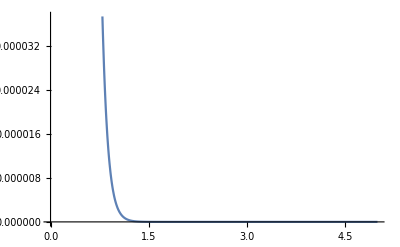

```mathematica
A2Bx[a_,d_,c_,j_,x_]:= (2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
Plot[A2Bx[5.3*Exp[-10*0.501],(1+0.103*9),0.052(1-7.73/10),2.16,x],{x,0,5}]
```

```mathematica
FourierA2bReel1minuskBYeta[b2_,P1_,etamin_, etamax_, bminForFit_, etafit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B,fourierA2Bforx,fourierREA2Bforx},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print[etamin,"",etamax," are SELECTED for fit!"];
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B; 
Print[modelfitA2B[,,,{a,c,d,f,k,j}]];
Print[{modelfitA2B[,,,{a,c, d,f,k,j}],"{a,c,d,f,k,j}",OutputForm[fitParasA2B],OutputForm[chisqfitA2B]}];
Print[ "  = ",b2, "  = ",P1];
b2II = b2*fitParasA2B[[1]]/fitParasA2B[[1]];
II= fitParasA2B[[1]]/fitParasA2B[[1]];
fitaA2B =fitParasA2B[[1]];
fitcA2B=fitParasA2B[[2]];
fitdA2B =fitParasA2B[[3]];
fitfA2B =fitParasA2B[[4]];
fitkA2B =fitParasA2B[[5]];
fitjA2B =fitParasA2B[[6]];
(*
A2BReprefactorbsq=(PowerJackk[etafit,fithA2B]*fitdA2B);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, A2BReprefactorbsq_, fA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))-A2BReprefactorbsq*b2]*Exp[-fA2B*etafit]*reducedr;

Print["",etafit," is SELECTED for plot!"];
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, A2BReprefactorbsq, fitfA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];*)
];
```

```mathematica
FourierA2bReel1minuskBYeta[9,-1,7, 10, 3,10]
```

3 are SELECTED for fit!

710 are SELECTED for fit!

a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j

{a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j,{a,c,d,f,k,j},{⟨5.3(12)⟩_(2902J), ⟨0.052(21)⟩_(2902J), ⟨0.103(29)⟩_(2902J), ⟨0.501(15)⟩_(2902J), ⟨7.73(67)⟩_(2902J), ⟨2.16(21)⟩_(2902J)},1.1098}

= 9  = -1

```mathematica
FourierA2bReel1minuskBYeta[9,-2,7, 10, 3,10]
```

3 are SELECTED for fit!

710 are SELECTED for fit!

a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j

{a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j,{a,c,d,f,k,j},{⟨3.4(15)⟩_(2902J), ⟨0.030(22)⟩_(2902J), ⟨0.046(33)⟩_(2902J), ⟨0.510(29)⟩_(2902J), ⟨7.3(12)⟩_(2902J), ⟨3.1(11)⟩_(2902J)},0.847695}

= 9  = -2

```mathematica
FourierA2bReel1minuskBYeta[9,-3,5, 10, 3,10]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j

{a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j,{a,c,d,f,k,j},{⟨1.59(46)⟩_(2902J), ⟨0.0087(87)⟩_(2902J), ⟨0.009 ± 0.011⟩_(2902J), ⟨0.513(37)⟩_(2902J), ⟨4.94(45)⟩_(2902J), ⟨1.8(83)⟩_(2902J)},1.01227}

= 9  = -3

```mathematica
FourierA2bReel1minuskBYeta[9,-4,5, 10, 3,10]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j

{a ⅇ^(-f η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j,{a,c,d,f,k,j},                                                                                                        -6
{⟨0.97(55)⟩_(2902J), ⟨0.001000021(82)⟩_(2902J), ⟨440(580) × 10  ⟩_(2902J), ⟨0.472(74)⟩_(2902J), ⟨4.39(67)⟩_(2902J), ⟨105(67)⟩_(2902J)},0.53945}

= 9  = -4

```mathematica
PrintxA2B[etafit_]:=Module[{fourieA2Bxforplot},
P1 = -4;
(*aa = fitaA2B *ExpJackk[fitfA2B,-etafit];
dd=II+fitdA2B*9;
cc=(fitcA2B(II-fitkA2B/etafit))/(P1^2);*)
aa = fitaA2B ;
dd=II+fitdA2B*9;
cc=(fitcA2B)/(P1^2);

fourierA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{aa,dd,cc,fitjA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];];
```

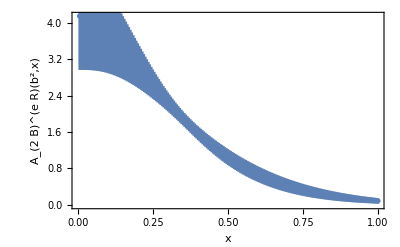

```mathematica
PrintxA2B[10]
```

10 is SELECTED for plot!

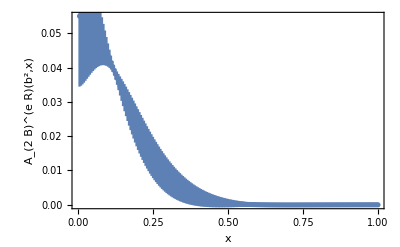

```mathematica
FourierA2bReel1minuskBYeta[10]
```

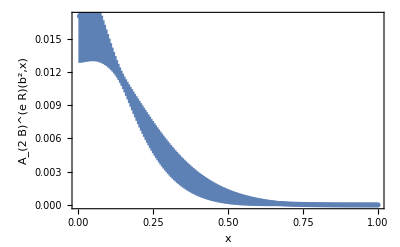

```mathematica
FourierA2bReel1minuskBYeta[12]
```

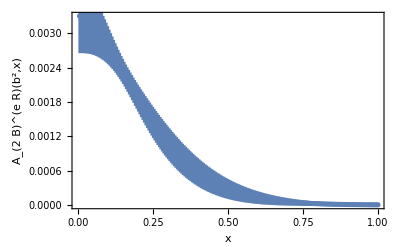

```mathematica
FourierA2bReel1minuskBYeta[15]
```

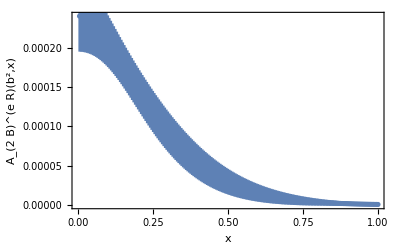

```mathematica
FourierA2bReel1minuskBYeta[20]
```

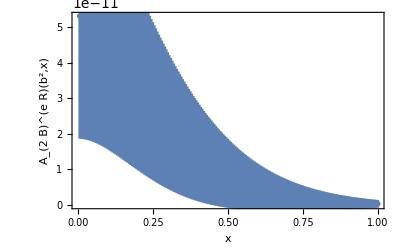

```mathematica
FourierA2bReel1minuskBYeta[50]
```

```mathematica
Print["PL = -2"]
```

PL = -2

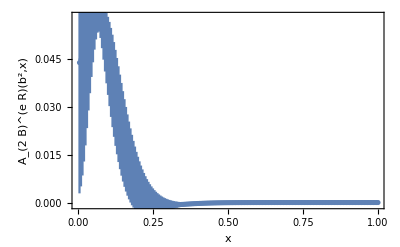

```mathematica
PrintxA2B[10]
```

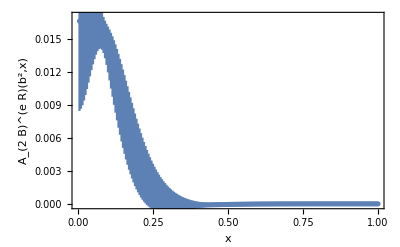

```mathematica
PrintxA2B[12]
```

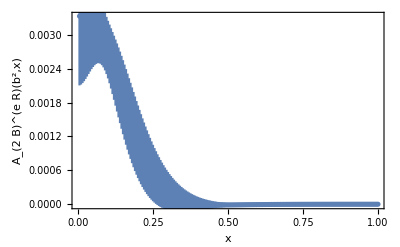

```mathematica
PrintxA2B[15]
```

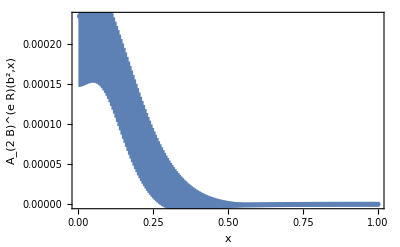

```mathematica
PrintxA2B[20]
```

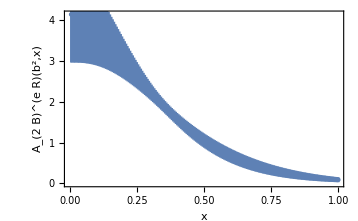

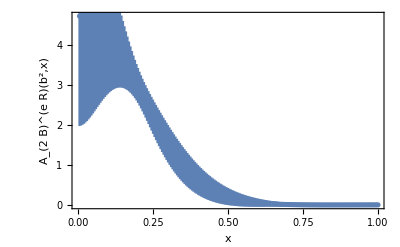

```mathematica
PrintxA2B[10]
```

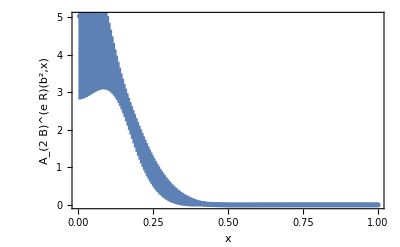

```mathematica
PrintxA2B[10]
```

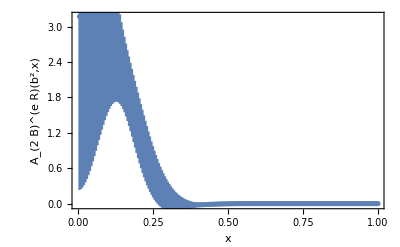

```mathematica
PrintxA2B[10]
```

```mathematica
FitetarangeListA12B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];


modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k_}]:=a*Exp[-0.5*x1]*Exp[-(d+c*(1-(k*x1^(-1))))*x2^2-d*x3^2];
fitJKA2B=JackknifeFit4D[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k}],{{a,5.3},{c,0.052},{d,0.103},{k,7.73}},{n,bL,bT},modelfitA2B];
AppendTo[results,{modelfitA2B[,,,{a,c, d,k}],"{a,c,d,k}",OutputForm[FitParameters/.fitJKA2B],OutputForm[chisquareDoF/.fitJKA2B]}];

Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeListA12B[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.5 η+(-d-c (1-k/η)) b_L^2-d b_T^2) | {a,c,d,k} |                                                                                                                                              3
{⟨-0.51(13)⟩_(2902J), ⟨0.0176(99)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨-11(10) × 10 ⟩_(2902J)} | 0.67382

```mathematica
FitetarangeListA12B[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.5 η+(-d-c (1-k/η)) b_L^2-d b_T^2) | {a,c,d,k,j} | {⟨5.0730(28)⟩_(2902J), ⟨6.7790(97)⟩_(2902J), ⟨1.811(13)⟩_(2902J), ⟨7.573(17)⟩_(2902J), ⟨2.6⟩_(2902J)} | 5.84683

```mathematica
FitetarangeListA12B[1,-1,7,10]
```

Gaussian-type fit for Re  for =-1
1 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.5 η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,k,j} | {⟨5.0142(62)⟩_(2902J), ⟨4.628(14)⟩_(2902J), ⟨1.896(11)⟩_(2902J), ⟨7.832(38)⟩_(2902J), ⟨12.301(42)⟩_(2902J)} | 15.9095

```mathematica
FitetarangeListA12B[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-0.5 η) (1+(d+c (1-k/η)) b_L^2+d b_T^2)^-j | {a,c,d,k,j} | {⟨5.1774(13)⟩_(2902J), ⟨5.324(25)⟩_(2902J), ⟨0.7557(45)⟩_(2902J), ⟨7.179(24)⟩_(2902J), ⟨8.425(33)⟩_(2902J)} | 5.84683

```mathematica
FitetarangeListA12B[3,-1,7,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
710 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF
a ⅇ^(-f η-c b_L^2-d b_T^2) | {a,c,d,f} | {⟨-0.72(53)⟩_(2902J), ⟨0.080(19)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨0.568(82)⟩_(2902J)} | 0.611894
a ⅇ^(-f η-c b_L^2-d η b_T^2) | {a,c,d,f} | {⟨-0.27(19)⟩_(2902J), ⟨0.080(19)⟩_(2902J), ⟨0.0088(18)⟩_(2902J), ⟨0.436(81)⟩_(2902J)} | 0.59739
a ⅇ^(-f η-c η b_L^2-d b_T^2) | {a,c,d,f} | {⟨-0.50(37)⟩_(2902J), ⟨0.0105(26)⟩_(2902J), ⟨0.065(13)⟩_(2902J), ⟨0.523(83)⟩_(2902J)} | 0.645856
a ⅇ^(-f η-c η^g b_L^2-d b_T^2) | {a,c,d,f,g} | {⟨-1.16(91)⟩_(2902J), ⟨-1.2(21)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨0.633(89)⟩_(2902J), ⟨-1.3(12)⟩_(2902J)} | 0.594605
a ⅇ^(-f η^h-c η^g b_L^2-d b_T^2) | {a,c,d,f,g,h} | {⟨-0.06 ± 0.11⟩_(2902J), ⟨1.6(19)⟩_(2902J), ⟨0.067(13)⟩_(2902J), ⟨-0.039(71)⟩_(2902J), ⟨-2.9(13)⟩_(2902J), ⟨1.7(11)⟩_(2902J)} | 0.675101
a ⅇ^(-f η-d b_T^2) (1+η)^(-c b_L^2) | {a,c,d,f} | {⟨-0.62(45)⟩_(2902J), ⟨0.0373(87)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨0.549(82)⟩_(2902J)} | 0.622948
a ⅇ^(-f η-d b_T^2) (1+g η)^(-c b_L^2) | {a,c,d,f,g} | {⟨-0.35(16)⟩_(2902J), ⟨1.45(97)⟩_(2902J), ⟨0.0751(21)⟩_(2902J), ⟨0.469(17)⟩_(2902J), ⟨-1.35(88)⟩_(2902J)} |                               2                              2                             2                              2                              2                              2                              2                              2                              2                              2                              2                               2                               2                               2                               2                               2                 -6           2                              2                                   2                              2                              2                             2                              2                             2                            2                             2                             2                             2                             2                             2                             2                           2                             2                             2                             2                             2                                   2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                           2                            2                            2                            2                            2                           2                            2                            2                            2                            2                            2                            2                                  2                            2                            2                            2                            2                            2                            2                                  2                            2                                  2                            2                            2                            2                            2                            2                            2                            2                            2                            2                                  2                                 2                            2                                  2                                 2                           2                            2                                  2                            2                            2                                 2                            2                                  2                                 2                           2                                  2                                 2                            2                                  2                                  2                                 2                                  2                                 2                                 2
1.99999 (-0.0009479 + {}[[2]])  + 2. (-0.000565175 + {}[[2]])  + 2. (-0.00055886 + {}[[2]])  + 1. (-0.000351163 + {}[[2]])  + 2. (-0.000249496 + {}[[2]])  + 2. (-0.000229472 + {}[[2]])  + 2. (-0.000195227 + {}[[2]])  + 2. (-0.000157386 + {}[[2]])  + 1. (-0.000152784 + {}[[2]])  + 2. (-0.000150152 + {}[[2]])  + 2. (-0.000147219 + {}[[2]])  + 2. (-0.0000744936 + {}[[2]])  + 2. (-0.0000642781 + {}[[2]])  + 2. (-0.0000457713 + {}[[2]])  + 2. (-0.0000315552 + {}[[2]])  + 2. (-0.0000292184 + {}[[2]])  + 1. (7.02521 10   + {}[[2]])  + 2. (0.0000148163 + {}[[2]])  + 1.99999 (0.0000496438 + {}[[2]])  + 2. (0.0000513284 + {}[[2]])  + 1. (0.0000578103 + {}[[2]])  + 1. (0.000065958 + {}[[2]])  + 2. (0.0000907766 + {}[[2]])  + 2. (0.000108855 + {}[[2]])  + 2. (0.00012745 + {}[[2]])  + 1. (0.000132023 + {}[[2]])  + 2. (0.000136444 + {}[[2]])  + 2. (0.000140185 + {}[[2]])  + 2. (0.000146709 + {}[[2]])  + 2. (0.000157723 + {}[[2]])  + 2. (0.000160301 + {}[[2]])  + 2. (0.0001883 + {}[[2]])  + 2. (0.000195461 + {}[[2]])  + 1. (0.000239376 + {}[[2]])  + 1. (0.000281749 + {}[[2]])  + 2. (0.000298604 + {}[[2]])  + 0.999999 (0.000302947 + {}[[2]])  + 2. (0.000336578 + {}[[2]])  + 1. (0.000388309 + {}[[2]])  + 2. (0.000412749 + {}[[2]])  + 2. (0.000418619 + {}[[2]])  + 2. (0.000428326 + {}[[2]])  + 2. (0.000443924 + {}[[2]])  + 1. (0.000482622 + {}[[2]])  + 2. (0.000491743 + {}[[2]])  + 1. (0.000496473 + {}[[2]])  + 1. (0.000502378 + {}[[2]])  + 2. (0.000507672 + {}[[2]])  + 1. (0.000539856 + {}[[2]])  + 2. (0.000666146 + {}[[2]])  + 1. (0.000689996 + {}[[2]])  + 2. (0.000730112 + {}[[2]])  + 1. (0.000814863 + {}[[2]])  + 2. (0.000823679 + {}[[2]])  + 2. (0.000927294 + {}[[2]])  + 2. (0.000962963 + {}[[2]])  + 2. (0.000984958 + {}[[2]])  + 1. (0.0010073 + {}[[2]])  + 1. (0.00101563 + {}[[2]])  + 2. (0.00105806 + {}[[2]])  + 2. (0.00108028 + {}[[2]])  + 2. (0.00109253 + {}[[2]])  + 1. (0.0011019 + {}[[2]])  + 2. (0.00120961 + {}[[2]])  + 2. (0.00121421 + {}[[2]])  + 2. (0.00126206 + {}[[2]])  + 2. (0.00128515 + {}[[2]])  + 2. (0.00132064 + {}[[2]])  + 2. (0.00132364 + {}[[2]])  + 0.999999 (0.00138631 + {}[[2]])  + 2. (0.00142638 + {}[[2]])  + 1. (0.00144096 + {}[[2]])  + 1. (0.00144282 + {}[[2]])  + 1. (0.00156298 + {}[[2]])  + 2. (0.00157673 + {}[[2]])  + 2. (0.00164589 + {}[[2]])  + 0.999999 (0.00174315 + {}[[2]])  + 2. (0.00178666 + {}[[2]])  + 0.999999 (0.00179104 + {}[[2]])  + 2. (0.00190624 + {}[[2]])  + 2. (0.00203221 + {}[[2]])  + 1. (0.00203775 + {}[[2]])  + 1. (0.00205054 + {}[[2]])  + 1. (0.00217365 + {}[[2]])  + 1. (0.00241411 + {}[[2]])  + 2. (0.00241775 + {}[[2]])  + 2. (0.00250423 + {}[[2]])  + 2. (0.00252341 + {}[[2]])  + 0.999999 (0.00253745 + {}[[2]])  + 1.99999 (0.00254198 + {}[[2]])  + 2. (0.00275231 + {}[[2]])  + 0.999999 (0.00294379 + {}[[2]])  + 1.99999 (0.00295833 + {}[[2]])  + 2. (0.0032506 + {}[[2]])  + 2. (0.00340833 + {}[[2]])  + 0.999999 (0.00349604 + {}[[2]])  + 1. (0.00349832 + {}[[2]])  + 2. (0.00373627 + {}[[2]])  + 1.99999 (0.00378584 + {}[[2]])  + 2. (0.00378869 + {}[[2]])  + 0.999999 (0.00380382 + {}[[2]])  + 1.99999 (0.00389559 + {}[[2]])  + 2. (0.0043002 + {}[[2]])  + 0.999999 (0.00466676 + {}[[2]])  + 1.99999 (0.00486197 + {}[[2]])  + 2. (0.00495378 + {}[[2]])  + 0.999998 (0.00552756 + {}[[2]])  + 0.999999 (0.00589327 + {}[[2]])  + 1.99998 (0.00615657 + {}[[2]])  + 0.999999 (0.00696764 + {}[[2]])  + 0.999998 (0.0108299 + {}[[2]])  + 0.999998 (0.0117538 + {}[[2]])
---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       179
a ⅇ^(-f η-(c η b_L^2)/(1+η)-d b_T^2) | {a,c,d,f} | {⟨-0.69(51)⟩_(2902J), ⟨0.091(21)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨0.563(82)⟩_(2902J)} | 0.614577
a ⅇ^(-f η^g-d b_T^2) (1+η)^(-c b_L^2) | {a,c,d,f,g} | {⟨1.09(15)⟩_(2902J), ⟨0.0338(87)⟩_(2902J), ⟨0.070(13)⟩_(2902J), ⟨-0.806(89)⟩_(2902J), ⟨25.8(42)⟩_(2902J)} | 19.0183
a ⅇ^(-f η^g-(c η b_L^2)/(1+η)-d b_T^2) | {a,c,d,f,g} | {⟨0.041(39)⟩_(2902J), ⟨0.091(21)⟩_(2902J), ⟨0.066(13)⟩_(2902J), ⟨-0.061(24)⟩_(2902J), ⟨4.4(12)⟩_(2902J)} | 0.630504
a ⅇ^(-f η-c η^g b_L^2-d b_T^2) η^h | {a,c,d,f,g,h} | {⟨0.072(16)⟩_(2902J), ⟨11.3(23)⟩_(2902J), ⟨0.070(13)⟩_(2902J), ⟨3.48(86)⟩_(2902J), ⟨-9.5(15)⟩_(2902J), ⟨19.5(65)⟩_(2902J)} | 1.26274
a ⅇ^(-f η-d b_T^2) η^h (1+c η^g b_L^2)^-j | {a,c,d,f,g,h,j} | {⟨1.5(25)⟩_(2902J), ⟨-0.0082(88)⟩_(2902J), ⟨0.0698(24)⟩_(2902J), ⟨0.22(13)⟩_(2902J), ⟨1.60(45)⟩_(2902J), ⟨-1.64(96)⟩_(2902J), ⟨0.88(23)⟩_(2902J)} |                                         2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                               2                               2                               2                              2                                   2                              2                              2                             2                            2                             2                             2                             2                             2                             2                           2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                                 2                            2                                 2                            2                            2                                 2                            2                                 2                                 2                            2                                 2
778.444 + 1.99999 (-0.0009479 + {}[[2]])  + 2. (-0.000565175 + {}[[2]])  + 2. (-0.00055886 + {}[[2]])  + 2. (-0.000249496 + {}[[2]])  + 2. (-0.000229472 + {}[[2]])  + 2. (-0.000195227 + {}[[2]])  + 2. (-0.000157386 + {}[[2]])  + 2. (-0.000150152 + {}[[2]])  + 2. (-0.000147219 + {}[[2]])  + 2. (-0.0000744936 + {}[[2]])  + 2. (-0.0000642781 + {}[[2]])  + 2. (-0.0000457713 + {}[[2]])  + 2. (-0.0000315552 + {}[[2]])  + 2. (-0.0000292184 + {}[[2]])  + 2. (0.0000148163 + {}[[2]])  + 1.99999 (0.0000496438 + {}[[2]])  + 2. (0.0000513284 + {}[[2]])  + 2. (0.0000907766 + {}[[2]])  + 2. (0.000108855 + {}[[2]])  + 2. (0.00012745 + {}[[2]])  + 2. (0.000136444 + {}[[2]])  + 2. (0.000140185 + {}[[2]])  + 2. (0.000146709 + {}[[2]])  + 2. (0.000157723 + {}[[2]])  + 2. (0.000160301 + {}[[2]])  + 2. (0.0001883 + {}[[2]])  + 2. (0.000195461 + {}[[2]])  + 2. (0.000298604 + {}[[2]])  + 2. (0.000336578 + {}[[2]])  + 2. (0.000412749 + {}[[2]])  + 2. (0.000418619 + {}[[2]])  + 2. (0.000428326 + {}[[2]])  + 2. (0.000443924 + {}[[2]])  + 2. (0.000491743 + {}[[2]])  + 2. (0.000507672 + {}[[2]])  + 2. (0.000666146 + {}[[2]])  + 2. (0.000730112 + {}[[2]])  + 2. (0.000823679 + {}[[2]])  + 2. (0.000927294 + {}[[2]])  + 2. (0.000962963 + {}[[2]])  + 2. (0.000984958 + {}[[2]])  + 2. (0.00105806 + {}[[2]])  + 2. (0.00108028 + {}[[2]])  + 2. (0.00109253 + {}[[2]])  + 2. (0.00120961 + {}[[2]])  + 2. (0.00121421 + {}[[2]])  + 2. (0.00126206 + {}[[2]])  + 2. (0.00128515 + {}[[2]])  + 2. (0.00132064 + {}[[2]])  + 2. (0.00132364 + {}[[2]])  + 2. (0.00142638 + {}[[2]])  + 2. (0.00157673 + {}[[2]])  + 2. (0.00164589 + {}[[2]])  + 2. (0.00178666 + {}[[2]])  + 2. (0.00190624 + {}[[2]])  + 2. (0.00203221 + {}[[2]])  + 2. (0.00241775 + {}[[2]])  + 2. (0.00250423 + {}[[2]])  + 2. (0.00252341 + {}[[2]])  + 1.99999 (0.00254198 + {}[[2]])  + 2. (0.00275231 + {}[[2]])  + 1.99999 (0.00295833 + {}[[2]])  + 2. (0.00340833 + {}[[2]])  + 2. (0.00373627 + {}[[2]])  + 1.99999 (0.00378584 + {}[[2]])  + 2. (0.00378869 + {}[[2]])  + 1.99999 (0.00389559 + {}[[2]])  + 1.99999 (0.00486197 + {}[[2]])  + 2. (0.00495378 + {}[[2]])  + 1.99998 (0.00615657 + {}[[2]])
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          177
a ⅇ^(-f η-d b_T^2) (1+c η^g b_L^2)^-j | {a,c,d,f,g,j} |                                                                                                                                                                                                                                  3
{⟨-1.24(96)⟩_(2902J), ⟨-0.54(52)⟩_(2902J), ⟨0.067(13)⟩_(2902J), ⟨0.642(91)⟩_(2902J), ⟨-1.3(12)⟩_(2902J), ⟨-1.78(43) × 10 ⟩_(2902J)} | 0.593287
a ⅇ^(-f η-c η^g b_L^2) (1+d b_T^2)^-j | {a,c,d,f,g,j} | {⟨-1.9(23)⟩_(2902J), ⟨-1.0(20)⟩_(2902J), ⟨0.052(82)⟩_(2902J), ⟨0.636(90)⟩_(2902J), ⟨-1.2(11)⟩_(2902J), ⟨1.4(12)⟩_(2902J)} | 0.538501
a ⅇ^(-f η) (1+c η^g b_L^2)^-l (1+d b_T^2)^-k | {a,c,d,f,g,k,l} | {⟨-2.0(22)⟩_(2902J), ⟨-0.31(43)⟩_(2902J), ⟨0.054(79)⟩_(2902J), ⟨0.639(90)⟩_(2902J), ⟨-1.2(12)⟩_(2902J), ⟨1.4(11)⟩_(2902J), ⟨-600(260)⟩_(2902J)} | 0.532917
a ⅇ^(-f η) η^h (1+c η^g b_L^2+d b_T^2)^-j | {a,c,d,f,g,h,j} | {⟨-0.2 ± 1.4⟩_(2902J), ⟨-0.0112(74)⟩_(2902J), ⟨0.009 ± 0.031⟩_(2902J), ⟨0.313(68)⟩_(2902J), ⟨1.35(34)⟩_(2902J), ⟨-1.05(53)⟩_(2902J), ⟨1.13(17)⟩_(2902J)} |                                         2                              2                             2                              2                              2                              2                              2                              2                              2                               2                               2                               2                               2                               2                              2                                   2                              2                              2                             2                            2                             2                             2                             2                             2                             2                           2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                            2                                 2                                 2                            2                            2                                 2                            2                                 2                                 2                            2                                 2
120.888 + 1.99999 (-0.0009479 + {}[[2]])  + 2. (-0.000565175 + {}[[2]])  + 2. (-0.00055886 + {}[[2]])  + 2. (-0.000249496 + {}[[2]])  + 2. (-0.000229472 + {}[[2]])  + 2. (-0.000195227 + {}[[2]])  + 2. (-0.000157386 + {}[[2]])  + 2. (-0.000150152 + {}[[2]])  + 2. (-0.000147219 + {}[[2]])  + 2. (-0.0000744936 + {}[[2]])  + 2. (-0.0000642781 + {}[[2]])  + 2. (-0.0000457713 + {}[[2]])  + 2. (-0.0000315552 + {}[[2]])  + 2. (-0.0000292184 + {}[[2]])  + 2. (0.0000148163 + {}[[2]])  + 1.99999 (0.0000496438 + {}[[2]])  + 2. (0.0000513284 + {}[[2]])  + 2. (0.0000907766 + {}[[2]])  + 2. (0.000108855 + {}[[2]])  + 2. (0.00012745 + {}[[2]])  + 2. (0.000136444 + {}[[2]])  + 2. (0.000140185 + {}[[2]])  + 2. (0.000146709 + {}[[2]])  + 2. (0.000157723 + {}[[2]])  + 2. (0.000160301 + {}[[2]])  + 2. (0.0001883 + {}[[2]])  + 2. (0.000195461 + {}[[2]])  + 2. (0.000298604 + {}[[2]])  + 2. (0.000336578 + {}[[2]])  + 2. (0.000412749 + {}[[2]])  + 2. (0.000418619 + {}[[2]])  + 2. (0.000428326 + {}[[2]])  + 2. (0.000443924 + {}[[2]])  + 2. (0.000491743 + {}[[2]])  + 2. (0.000507672 + {}[[2]])  + 2. (0.000666146 + {}[[2]])  + 2. (0.000730112 + {}[[2]])  + 2. (0.000823679 + {}[[2]])  + 2. (0.000927294 + {}[[2]])  + 2. (0.000962963 + {}[[2]])  + 2. (0.000984958 + {}[[2]])  + 2. (0.00105806 + {}[[2]])  + 2. (0.00109253 + {}[[2]])  + 2. (0.00120961 + {}[[2]])  + 2. (0.00121421 + {}[[2]])  + 2. (0.00126206 + {}[[2]])  + 2. (0.00128515 + {}[[2]])  + 2. (0.00132064 + {}[[2]])  + 2. (0.00132364 + {}[[2]])  + 2. (0.00142638 + {}[[2]])  + 2. (0.00164589 + {}[[2]])  + 2. (0.00178666 + {}[[2]])  + 2. (0.00190624 + {}[[2]])  + 2. (0.00241775 + {}[[2]])  + 2. (0.00250423 + {}[[2]])  + 2. (0.00252341 + {}[[2]])  + 1.99999 (0.00254198 + {}[[2]])  + 1.99999 (0.00295833 + {}[[2]])  + 2. (0.00340833 + {}[[2]])  + 2. (0.00373627 + {}[[2]])  + 1.99999 (0.00378584 + {}[[2]])  + 2. (0.00378869 + {}[[2]])  + 1.99999 (0.00389559 + {}[[2]])  + 1.99999 (0.00486197 + {}[[2]])  + 2. (0.00495378 + {}[[2]])  + 1.99998 (0.00615657 + {}[[2]])
---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                177
a ⅇ^(-f η) (1+c η^g b_L^2+d b_T^2)^-j | {a,c,d,f,g,j} | {⟨-300(18)⟩_(2902J), ⟨93.0(53)⟩_(2902J), ⟨15.60(96)⟩_(2902J), ⟨-6.57(49)⟩_(2902J), ⟨8.5(20)⟩_(2902J), ⟨-27.3(36)⟩_(2902J)} |                                      2                              2                              2                              2                               2                               2                               2                               2                 -6           2                              2                             2                              2                             2                             2                             2                           2                             2                             2                             2                             2                                   2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                           2                            2                            2                            2                           2                            2                            2                            2                                  2                            2                            2                            2                            2                            2                                  2                            2                            2                            2                            2                            2                            2                           2                                  2                            2                                  2                           2                                  2
8445.52 + 1. (-0.000351163 + {}[[2]])  + 2. (-0.000229472 + {}[[2]])  + 1. (-0.000152784 + {}[[2]])  + 2. (-0.000150152 + {}[[2]])  + 2. (-0.0000744936 + {}[[2]])  + 2. (-0.0000642781 + {}[[2]])  + 2. (-0.0000315552 + {}[[2]])  + 2. (-0.0000292184 + {}[[2]])  + 1. (7.02521 10   + {}[[2]])  + 1. (0.0000578103 + {}[[2]])  + 1. (0.000065958 + {}[[2]])  + 2. (0.0000907766 + {}[[2]])  + 1. (0.000132023 + {}[[2]])  + 2. (0.000146709 + {}[[2]])  + 2. (0.000157723 + {}[[2]])  + 2. (0.0001883 + {}[[2]])  + 2. (0.000195461 + {}[[2]])  + 1. (0.000239376 + {}[[2]])  + 1. (0.000281749 + {}[[2]])  + 2. (0.000298604 + {}[[2]])  + 0.999999 (0.000302947 + {}[[2]])  + 2. (0.000336578 + {}[[2]])  + 1. (0.000388309 + {}[[2]])  + 2. (0.000412749 + {}[[2]])  + 2. (0.000428326 + {}[[2]])  + 2. (0.000443924 + {}[[2]])  + 1. (0.000482622 + {}[[2]])  + 1. (0.000496473 + {}[[2]])  + 1. (0.000502378 + {}[[2]])  + 2. (0.000507672 + {}[[2]])  + 1. (0.000539856 + {}[[2]])  + 1. (0.000689996 + {}[[2]])  + 1. (0.000814863 + {}[[2]])  + 2. (0.000823679 + {}[[2]])  + 2. (0.000927294 + {}[[2]])  + 2. (0.000962963 + {}[[2]])  + 2. (0.000984958 + {}[[2]])  + 1. (0.0010073 + {}[[2]])  + 1. (0.00101563 + {}[[2]])  + 2. (0.00105806 + {}[[2]])  + 2. (0.00108028 + {}[[2]])  + 1. (0.0011019 + {}[[2]])  + 2. (0.00120961 + {}[[2]])  + 2. (0.00128515 + {}[[2]])  + 2. (0.00132064 + {}[[2]])  + 0.999999 (0.00138631 + {}[[2]])  + 1. (0.00144096 + {}[[2]])  + 1. (0.00144282 + {}[[2]])  + 1. (0.00156298 + {}[[2]])  + 2. (0.00157673 + {}[[2]])  + 2. (0.00164589 + {}[[2]])  + 0.999999 (0.00179104 + {}[[2]])  + 2. (0.00203221 + {}[[2]])  + 1. (0.00203775 + {}[[2]])  + 1. (0.00205054 + {}[[2]])  + 1. (0.00217365 + {}[[2]])  + 1. (0.00241411 + {}[[2]])  + 2. (0.00275231 + {}[[2]])  + 2. (0.0032506 + {}[[2]])  + 0.999999 (0.00349604 + {}[[2]])  + 1. (0.00349832 + {}[[2]])  + 0.999999 (0.00380382 + {}[[2]])  + 2. (0.0043002 + {}[[2]])  + 0.999999 (0.00589327 + {}[[2]])
-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           178
a ⅇ^(-f η) (1+d (c η^g b_L^2+b_T^2))^-j | {a,c,d,f,g,j} |                                                         3
{⟨-546(39)⟩_(2902J), ⟨3.93(25) × 10 ⟩_(2902J), ⟨29.2(22)⟩_(2902J), ⟨20.2(13)⟩_(2902J), ⟨-413(26)⟩_(2902J), ⟨293(19)⟩_(2902J)} |                               2                              2                             2                              2                              2                              2                              2                              2                              2                              2                              2                               2                               2                               2                               2                               2                 -6           2                              2                                   2                              2                              2                             2                              2                             2                            2                             2                             2                             2                             2                             2                             2                           2                             2                             2                             2                             2                                   2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                             2                           2                            2                            2                            2                            2                           2                            2                            2                            2                            2                            2                            2                                  2                            2                            2                            2                            2                            2                            2                                  2                            2                                  2                            2                            2                            2                            2                            2                            2                            2                            2                            2                                  2                                 2                            2                                  2                                 2                           2                            2                                  2                            2                            2                                 2                            2                                  2                                 2                           2                                  2                                 2                            2                                  2                                  2                                 2                                  2                                 2                                 2
1.99999 (-0.0009479 + {}[[2]])  + 2. (-0.000565175 + {}[[2]])  + 2. (-0.00055886 + {}[[2]])  + 1. (-0.000351163 + {}[[2]])  + 2. (-0.000249496 + {}[[2]])  + 2. (-0.000229472 + {}[[2]])  + 2. (-0.000195227 + {}[[2]])  + 2. (-0.000157386 + {}[[2]])  + 1. (-0.000152784 + {}[[2]])  + 2. (-0.000150152 + {}[[2]])  + 2. (-0.000147219 + {}[[2]])  + 2. (-0.0000744936 + {}[[2]])  + 2. (-0.0000642781 + {}[[2]])  + 2. (-0.0000457713 + {}[[2]])  + 2. (-0.0000315552 + {}[[2]])  + 2. (-0.0000292184 + {}[[2]])  + 1. (7.02521 10   + {}[[2]])  + 2. (0.0000148163 + {}[[2]])  + 1.99999 (0.0000496438 + {}[[2]])  + 2. (0.0000513284 + {}[[2]])  + 1. (0.0000578103 + {}[[2]])  + 1. (0.000065958 + {}[[2]])  + 2. (0.0000907766 + {}[[2]])  + 2. (0.000108855 + {}[[2]])  + 2. (0.00012745 + {}[[2]])  + 1. (0.000132023 + {}[[2]])  + 2. (0.000136444 + {}[[2]])  + 2. (0.000140185 + {}[[2]])  + 2. (0.000146709 + {}[[2]])  + 2. (0.000157723 + {}[[2]])  + 2. (0.000160301 + {}[[2]])  + 2. (0.0001883 + {}[[2]])  + 2. (0.000195461 + {}[[2]])  + 1. (0.000239376 + {}[[2]])  + 1. (0.000281749 + {}[[2]])  + 2. (0.000298604 + {}[[2]])  + 0.999999 (0.000302947 + {}[[2]])  + 2. (0.000336578 + {}[[2]])  + 1. (0.000388309 + {}[[2]])  + 2. (0.000412749 + {}[[2]])  + 2. (0.000418619 + {}[[2]])  + 2. (0.000428326 + {}[[2]])  + 2. (0.000443924 + {}[[2]])  + 1. (0.000482622 + {}[[2]])  + 2. (0.000491743 + {}[[2]])  + 1. (0.000496473 + {}[[2]])  + 1. (0.000502378 + {}[[2]])  + 2. (0.000507672 + {}[[2]])  + 1. (0.000539856 + {}[[2]])  + 2. (0.000666146 + {}[[2]])  + 1. (0.000689996 + {}[[2]])  + 2. (0.000730112 + {}[[2]])  + 1. (0.000814863 + {}[[2]])  + 2. (0.000823679 + {}[[2]])  + 2. (0.000927294 + {}[[2]])  + 2. (0.000962963 + {}[[2]])  + 2. (0.000984958 + {}[[2]])  + 1. (0.0010073 + {}[[2]])  + 1. (0.00101563 + {}[[2]])  + 2. (0.00105806 + {}[[2]])  + 2. (0.00108028 + {}[[2]])  + 2. (0.00109253 + {}[[2]])  + 1. (0.0011019 + {}[[2]])  + 2. (0.00120961 + {}[[2]])  + 2. (0.00121421 + {}[[2]])  + 2. (0.00126206 + {}[[2]])  + 2. (0.00128515 + {}[[2]])  + 2. (0.00132064 + {}[[2]])  + 2. (0.00132364 + {}[[2]])  + 0.999999 (0.00138631 + {}[[2]])  + 2. (0.00142638 + {}[[2]])  + 1. (0.00144096 + {}[[2]])  + 1. (0.00144282 + {}[[2]])  + 1. (0.00156298 + {}[[2]])  + 2. (0.00157673 + {}[[2]])  + 2. (0.00164589 + {}[[2]])  + 0.999999 (0.00174315 + {}[[2]])  + 2. (0.00178666 + {}[[2]])  + 0.999999 (0.00179104 + {}[[2]])  + 2. (0.00190624 + {}[[2]])  + 2. (0.00203221 + {}[[2]])  + 1. (0.00203775 + {}[[2]])  + 1. (0.00205054 + {}[[2]])  + 1. (0.00217365 + {}[[2]])  + 1. (0.00241411 + {}[[2]])  + 2. (0.00241775 + {}[[2]])  + 2. (0.00250423 + {}[[2]])  + 2. (0.00252341 + {}[[2]])  + 0.999999 (0.00253745 + {}[[2]])  + 1.99999 (0.00254198 + {}[[2]])  + 2. (0.00275231 + {}[[2]])  + 0.999999 (0.00294379 + {}[[2]])  + 1.99999 (0.00295833 + {}[[2]])  + 2. (0.0032506 + {}[[2]])  + 2. (0.00340833 + {}[[2]])  + 0.999999 (0.00349604 + {}[[2]])  + 1. (0.00349832 + {}[[2]])  + 2. (0.00373627 + {}[[2]])  + 1.99999 (0.00378584 + {}[[2]])  + 2. (0.00378869 + {}[[2]])  + 0.999999 (0.00380382 + {}[[2]])  + 1.99999 (0.00389559 + {}[[2]])  + 2. (0.0043002 + {}[[2]])  + 0.999999 (0.00466676 + {}[[2]])  + 1.99999 (0.00486197 + {}[[2]])  + 2. (0.00495378 + {}[[2]])  + 0.999998 (0.00552756 + {}[[2]])  + 0.999999 (0.00589327 + {}[[2]])  + 1.99998 (0.00615657 + {}[[2]])  + 0.999999 (0.00696764 + {}[[2]])  + 0.999998 (0.0108299 + {}[[2]])  + 0.999998 (0.0117538 + {}[[2]])
---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       178